# MATH 263 Numerical differential equations

Ethan Smith

## Lecture 8: Higher order IVPs 25 MAR 2021

## Assigned reading for next time.

Zill, Section 9.5.

## Method implementations.

Disclaimer: The implementations below are not efficient in Mathematica, but they have been chosen for pedagogical reasons.

```mathematica
euler[f_,a_,b_,y0_,n_]:=Module[{x,y,h=N[(b-a)/n]},
{x[0],y[0]} =N[ {a,y0}];
Do[
x[i+1]=x[i]+h;
y[i+1]=y[i]+h*f[x[i],y[i]];,
{i,0,n-1}
];
Return[Table[{x[i],y[i]},{i,0,n}]]
];
```

```mathematica
heun[f_,a_,b_,y0_,n_]:=Module[{x,y,h=N[(b-a)/n],k1,k2,w1=0.5,w2=0.5},
{x[0],y[0]} = N[{a,y0}];
Do[
k1=f[x[i],y[i]];
k2=f[x[i]+h,y[i]+h*k1];
x[i+1]=x[i]+h;
y[i+1]=y[i]+h*(w1*k1 + w2*k2);,
{i,0,n-1}
];
Return[Table[{x[i],y[i]},{i,0,n}]]
];
```

```mathematica
rk4[f_,a_,b_,y0_,n_]:=Module[{x,y,h=N[(b-a)/n], k1, k2, k3, k4, w1=1./6, w2=1./3, w3=1./3,w4=1./6},
{x[0],y[0]} = N[{a,y0}];
Do[
k1=f[x[i],y[i]];
k2=f[x[i]+0.5*h,y[i]+0.5*h*k1];
k3=f[x[i]+0.5*h,y[i]+0.5*h*k2];
k4=f[x[i]+h,y[i]+h*k3];
x[i+1]=x[i]+h;
y[i+1]=y[i]+h*(w1*k1+w2*k2+w3*k3+w4*k4);,
{i,0,n-1}
];
Return[Table[{x[i],y[i]},{i,0,n}]];
];
```

```mathematica
ab2[f_,a_,b_,y0_,n_]:=Module[{x,y,h=N[(b-a)/n],f0,f1},
{{x[0],y[0]},{x[1],y[1]}}=heun[f,a,a+h,y0,1];
f1=f[x[0],y[0]];
Do[
f0=f[x[i],y[i]];
x[i+1]=x[i]+h;
y[i+1]=y[i]+h*(3*f0-f1)/2;
(*Shift f evals down to get ready for next step.  Could be done without actually moving the data, but not worth the effort here.*)
f1=f0;,
{i,1,n-1}
];
Return[Table[{x[i],y[i]},{i,0,n}]];
];
```

```mathematica
abm2[f_,a_,b_,y0_,n_]:=Module[{x,y,h=N[(b-a)/n],yhat,dy0,dy1,dy2},
{{x[0],y[0]},{x[1],y[1]}}=heun[f,a,a+h,y0,1];
dy2=f[x[0],y[0]];
Do[
dy1=f[x[i],y[i]];
x[i+1]=x[i]+h;
yhat=y[i]+h*(3*dy1-dy2)/2; (*predict*)
dy0=f[x[i+1],yhat];
y[i+1]=y[i]+h*(dy0+dy1)/2; (*correct*)
(*Shift f evals down to get ready for next step.  Could be done without actually moving the data, but not worth the effort here.*)
dy2=dy1;,
{i,1,n-1}
];
Return[Table[{x[i],y[i]},{i,0,n}]];
];
```

## Higher order initial value problems.

An mth order ODE in normal form is an equation of the form

y^(m)(x) = f(x,y,y', …, y^(m-1)).

An mth order IVP is an equation of this form together with m initial conditions of the form

y(x_0) =α_1, y'(x_0)=α_2, …, y^(m-1)(x_0)=α_m.

To numerically solve such a problem we introduce auxiliary variables (really functions) so as to express the problem as a first order system IVP.  Thus, we reduce the problem to one we already know how to solve.  More precisely, we let u_1=y, u_2=y', …, u_m=y^(m-1).  Then equation (1) is equivalent to the system

u_1'=u_2,
   u_2'=u_3,
⋮
u_(m-1)'=u_m,
                                      u_m'=f(x,u_1,u_2, …, u_m)

while the conditions (2) are equivalent to

u_1(x_0) =α_1, u_2(x_0)=α_2, …, u_m(x_0)=α_m.

In this way, we are able to compute a numerical solution y to (1) and (2) along with its lower order derivatives y', y'', …, y^(m-1).

## Example.

Consider the second-order initial-value problem

y’’ - 2y’ + 2y = e^(2x)sin(x), y(0)=-2/5, y’(0)=-3/5.

Solve the IVP exactly.

```mathematica
Clear[x,y]
f[x_,y_,Dy_]=2*Dy-2*y+Exp[2*x]*Sin[x];
{y0,Dy0}={-2/5,-3/5};
Y[x_]=y[x]/.DSolve[{y''[x]==f[x,y[x],y'[x]],y[0]==y0,y'[0]==Dy0},y[x],x][[1]]//FullSimplify
```

1/5 ⅇ^(2 x) (-2 Cos[x]+Sin[x])

Rewrite the second order IVP as a first order system and numerically solve the system over [0,1] using RK4 with step-size h=0.2.

Letting u_1=y, u_2=y', we write the IVP as

u_1'=u_2,
                                         u_2'=2 u_2-2 u_1+e^(2x)sin(x),
                                u_1(0)=-2/5, u_2(0)=-3/5.

{{0.,{-0.4,-0.6}},{0.2,{-0.525572,-0.640155}},{0.4,{-0.646642,-0.536586}},{0.6,{-0.721204,-0.144363}},{0.8,{-0.669786,0.772073}},{1.,{-0.353486,2.57899}}}

x_i | y_i | y(x_i) | |y(x_i)-y_i| | y_i' | y'(x_i) | |y'(x_i)-y_i'|
0. | -0.4 | -0.4 | 0. | -0.6 | -0.6 | 1.11022×10^-16
0.2 | -0.525572 | -0.525559 | 0.0000125459 | -0.640155 | -0.640149 | 6.20322×10^-6
0.4 | -0.646642 | -0.64661 | 0.0000313338 | -0.536586 | -0.536582 | 3.94634×10^-6
0.6 | -0.721204 | -0.721148 | 0.0000551517 | -0.144363 | -0.144383 | 0.0000201021
0.8 | -0.669786 | -0.669707 | 0.0000790477 | 0.772073 | 0.771984 | 0.0000890935
1. | -0.353486 | -0.353394 | 0.0000912613 | 2.57899 | 2.57875 | 0.00024072classical RK4 results

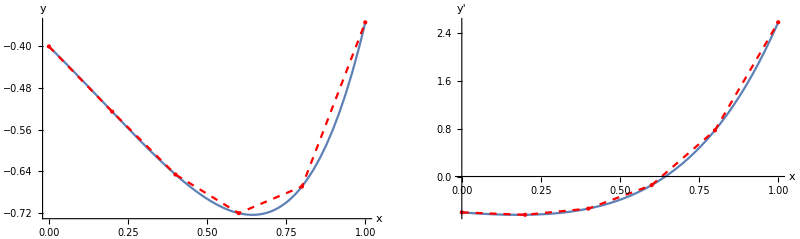

```mathematica
Clear[x,u,u1,u2];
u[x_]={u1[x],u2[x]};
F[x_,u_]:={u[[2]], f[x,u[[1]],u[[2]]]};
x0=0;
u0={y0,Dy0};
{a,b}={0,1};
h=0.2;
n=Round[(b-a)/h];
approxSoln=rk4[F,a,b,u0,n]

meshpt=approxSoln[[All,1]];
approxY=approxSoln[[All,2,1]];
exactY=Table[Y[meshpt[[i]]],{i,1,Length[meshpt]}];
yError=Abs[exactY-approxY];
approxDY=approxSoln[[All,2,2]];
exactDY=Table[Y'[meshpt[[i]]],{i,1,Length[meshpt]}];
dYError=Abs[exactDY-approxDY];

Labeled[TableForm[Join[{meshpt,approxY, exactY,yError,approxDY,exactDY,dYError}],TableDirections->Row,TableHeadings->{{"x_i","y_i","y(x_i)","|y(x_i)-y_i|","y_i'","y'(x_i)","|y'(x_i)-y_i'|"},None},TableSpacing->{2, 2}],"classical RK4 results",Top]

GraphicsRow[{
Show[
Plot[Y[x],{x,a,b},PlotRange->All],
ListPlot[Transpose[Join[{meshpt,approxY}]],PlotStyle->{Dashed,Red,PointSize[Large]},Joined->True,Mesh->All
],
PlotRange->All,
AxesLabel->{x,y},
ImageSize->Medium
],
Show[
Plot[Y'[x],{x,a,b},PlotRange->All],
ListPlot[Transpose[Join[{meshpt,approxDY}]],PlotStyle->{Dashed,Red,PointSize[Large]},Joined->True,Mesh->All],
PlotRange->All,
AxesLabel->{x,y'},
ImageSize->Medium
]
}]
```